```mathematica
SetDirectory[NotebookDirectory[]]
```

/work/Robin-Day/DNB/qd-acn/scattering_in_double-well/ipos-0.05

## Quantum dynamics analyst

### Basic constants

```mathematica
c=(Entity["PhysicalConstant","SpeedOfLight"]["Value"]//QuantityMagnitude)*100;(* Speed of light in cm/s *)
```

### Import data:

```mathematica
posCF=Import["corrF.dat","Table"][[2;;]];
dt=posCF[[1,1]];
ampData = Import["PAmp.dat","Table"][[2;;]];
xSpace=ampData[[1]];
(*potential=Import["potential.dat","Table"];*)
potential=Import["potential-MarcusModel.dat","Table"];
```

### Functions:

```mathematica
GetSpectrum[cf_List,dt_]:=
	Module[{signal,spectrum, wns, wnMax},
		signal=cf-Mean[cf];
		signal=Join[signal,ConstantArray[0,Length[signal]*10]];
		wns=Table[1/(Length[signal]*dt*1*^-15)/c*i,{i,0,Length[signal]-1}];
		spectrum = Abs[Fourier[signal]]^2;
		wnMax=Round[Length[signal]*dt*1*^-15*c*4500];
		Return[Transpose[{wns,spectrum}][[;;wnMax]]]
];

PlotSpectrum[data_List,xRange_List,label_String]:=
	Labeled[
	ListLinePlot[data,
		PlotRange->{xRange,All},
		Frame->True,
		FrameStyle->Directive[Black,14,FontFamily->"Helvetica",AbsoluteThickness[1.2]],
		ImageSize->250,
		GridLines->Automatic],
Style[#,Black,14,FontFamily->"Helvetica"]&/@{"Intensity","Wavenumber [cm^-1]",label},
{Left,Bottom,Top},RotateLabel->True]
PlotAmp[i_Integer,yRange_List]:=Module[{pltPot,pltAmp},
	pltPot=ListLinePlot[potential,
		PlotRange->{{-.25,.45},yRange},
		Frame->True,
		Axes->False,
		FrameStyle->Directive[12,Black,AbsoluteThickness[1.2],FontFamily->"Helvetica"],
		GridLines->Automatic,
		PlotStyle->Black];
	pltAmp=ListLinePlot[Transpose[{xSpace,ampData[[i+1,2;;]]/4}],
		PlotRange->All,
		Filling->Axis];
Labeled[
	Show[{pltPot,pltAmp},ImageSize->250,Epilog->{Text[Style["t = "<>ToString@Round@ampData[[i+1,1]]<>" fs",14,FontFamily->"Helvetica"],{.28,0.9*yRange[[2]]}]}],
	Style[#,14,FontFamily->"Helvetica"]&/@{"Energy [Hartree]","Distance [Bohr]"},{Left,Bottom},RotateLabel->True]
];
PlotKspace[i_]:=Labeled[ListLinePlot[
Transpose[{kspace,PAmpKspace[[i+1,2;;]]}],
PlotRange->{All,{0,100}},
Frame->True,
FrameStyle->Directive[Black,14,FontFamily->"Helvetica"],
GridLines->Automatic],
Style[#,Black,14,FontFamily->"Helvetica"]&/@{"|ψ(k)|^2","Momentum k"},
{Left,Bottom},RotateLabel->True]
ExportMovie[length_Integer,yMax_(*,stride_Integer*)]:=
Module[{toExport},
toExport=Table[ Rasterize[PlotAmp[i,{0,yMax}],ImageResolution->200],{i,1,length,2}];
Export["pAmpEvolution.mp4",toExport,FrameRate->20]
(*DeleteDirectory["movie-frames"]//Quiet;
CreateDirectory["movie-frames"]//Quiet;
Table[Export["movie-frames/frame-"<>ToString[i]<>".png",toExport[[i]]],{i,1,Length[toExport],stride}];*)
];
pltCoeffs[retrC_]:=Labeled[ListLinePlot[{MapAt[#^2&,retrC[[;;,{1,5}]],{All,2}],
MapAt[#^2&,retrC[[;;,{1,6}]],{All,2}]},
PlotRange->{{0,5},{0,1}},
Frame->True,
FrameStyle->Directive[Black,AbsoluteThickness[1.2],14,FontFamily->"Helvetica"],
PlotLegends->Placed[LineLegend[Style[#,Black,14,FontFamily->"Helvetica"]&/@{"Reflected","Transmitted"}],{Top,Right}]],
Style[#,Black,14,FontFamily->"Helvetica"]&/@{"Reflection/Transmission probability","Incident WP energy [eV]"},{Left,Bottom},RotateLabel->True]
```

### Analyses

#### Probability amplitude evolution

```mathematica
anim=Animate[PlotAmp[i,{0,.02}],{i,1,Length[ampData]-1,1},Deployed->True,AnimationRate->120,AnimationRunning->False]
```

```mathematica
(*Export["PAmp-anim.mp4",anim,ImageResolution->500]*)
```

#### Position-position autocorrelation function

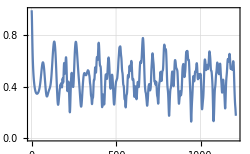
-Graphics-,|⟨ψ(0)|ψ(t)⟩|^2Time [fs]

```mathematica
posCFPlot=Labeled[
	ListLinePlot[posCF[[;;]],
		PlotRange->{All,All},
		Frame->True,
		FrameStyle->Directive[Black,12,FontFamily->"Helvetica",AbsoluteThickness[1.2]],
		ImageSize->250,
		GridLines->Automatic],
Style[#,Black,14,FontFamily->"Helvetica"]&/@{",|⟨ψ(0)|ψ(t)⟩|^2","Time [fs]"},
{Left,Bottom,Top},RotateLabel->True]
```

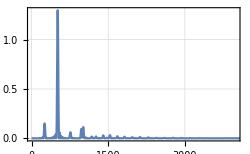
-Graphics-IntensityWavenumber [cm^-1]Position-position spectrum

```mathematica
posSpectrum=GetSpectrum[posCF[[;;,2]],dt];
PlotSpectrum[posSpectrum,{0,4000},"Position-position spectrum"]
```

#### Evolution of wavefunction in the momentum space

```mathematica
PAmpKspace = Import["PAmp-kspace.dat","Table"][[2;;]];
kspace = PAmpKspace[[1,;;]];
```

```mathematica
Animate[PlotKspace[i],{i,1,Length[PAmpKspace]-1,1},Deployed->True,AnimationRate->120,AnimationRunning->False]
```

#### Reflection and Transmission coefficients

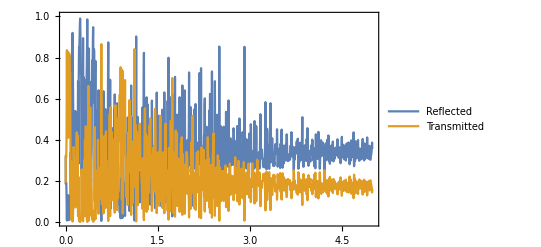
-Graphics-Reflection/Transmission probabilityIncident WP energy [eV]

```mathematica
retrCoef = Import["reflection-transmission_Coeffs.dat","Table"][[2;;]];
retrCF=Import["reflection-transmission_CFs.dat","Table"][[2;;]];
pltCoeffs[retrCoef]
```

#### Export movie and frames

```mathematica
ExportMovie[500,0.02]
```

pAmpEvolution.mp4

#### ET rate (attempt)...

```mathematica
Z[T_]:=1/(1-Exp[-Sqrt[1.21425/14.2480094]/(3.16681*^-6*T)])
ℏ=Entity["PhysicalConstant","ReducedPlanckConstant"]["Value"]//QuantityMagnitude;
e=Entity["PhysicalConstant","ElementaryCharge"]["Value"]//QuantityMagnitude;
kB=Entity["PhysicalConstant","BoltzmannConstant"]["Value"]//QuantityMagnitude;
```

```mathematica
kET=1/(ℏ*2*Pi*Z[300])*Sum[i[[1]]*Exp[-i[[2]]*e/kB/300],{i,retrCoef[[;;,{1,6}]]}]
```

2.71761×10^33

```mathematica
Sum[i[[1]]*Exp[-i[[2]]*e/kB/300],{i,retrCoef[[;;,{1,6}]]}]
```

1.8007

```mathematica
1/(ℏ*2*Pi*Z[300])
```

1.50919×10^33